# WENO Smooth Indicators

coded by Manuel Diaz, 2013.07.13
manuel.ade’at’gmail.com

```mathematica
Quit[]; (* Reset Mathematica Kernel *)
```

### Refs,

```mathematica
(* This Mathematica files is helpful to derive the coeficients to implement first and/or second order WENO based derivates following the ideas of the following references: *)
	(* 1. Shu; 'High order weighted essentially nonoscillatory schemes for convection dominated problems'. SIAM review 2009 *)
	(* 2. Jian and Shu; 'Efficient Implementation of weighted ENO schemes'. JCP 1996)
	(* 3. Also following ideas in the publication by RhysU@http://www.scribd.com/RhysU *)
```

```mathematica
(* INITIALIZE FUNCTIONS *)
	(* We need to build a list of uniform gridpoints with spacing Δx and fucntion values Subscript[f, i]. Use that list to build the j^th interpolating Polynomial for j ϵ {1,...,r} *)
```

### Continuous Case

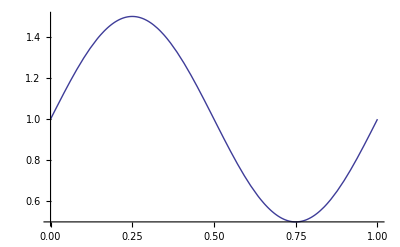

```mathematica
u[x_,t_]:= 0.5(2+Sin[2π x]);
sin =Plot[u[x,t],{x,0,1},PlotRange->Full]
```

Assume t = 0. Evaluate u[x,t] at discrete value points,

```mathematica
Table[Subscript[u, i]= With[{t=0,Δx =0.05},u[-1+i Δx,t]],{i,0,1/0.05}]
```

{1.,1.15451,1.29389,1.40451,1.47553,1.5,1.47553,1.40451,1.29389,1.15451,1.,0.845492,0.706107,0.595492,0.524472,0.5,0.524472,0.595492,0.706107,0.845492,1.}

### Discontinuous Case

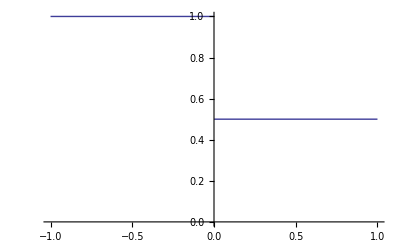

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

Assume t = 0. Evaluate u[x, t] at discrete value points,

```mathematica
Table[Subscript[u, i]= With[{t=0,Δx =0.1},u[-1+i Δx,t]],{i,0,2/0.1}]
```

{1,1,1,1,1,1,1,1,1,1,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

### Stencils and substencils

```mathematica
StencilPoints[r_]:=Table[{i Δx, Subscript[v, i]},{i,-(r-1),(r-1)}]
SubstencilPoints[r_,j_]:= Take[StencilPoints[r],{j,j+r-1}]
StencilPolynomial[r_,j_]:= Collect[InterpolatingPolynomial[SubstencilPoints[r,j],x],v,Simplify]
```

```mathematica
(* Check these functions will return the three expected interpolant values at Δx/2 for the r=3 case from [1], equations (2.1), 2.2) and (2.3) *)
```

### Testing Stencil and Substencil functions

```mathematica
StencilPoints[3]
```

{{-2 Δx,v_-2},{-Δx,v_-1},{0,v_0},{Δx,v_1},{2 Δx,v_2}}

```mathematica
StencilPolynomial[3,1]
```

(x (x+Δx) v_-2-(x+2 Δx) (2 x v_-1-(x+Δx) v_0))/(2 Δx^2)

```mathematica
D[StencilPolynomial[3,1],{x,2}] (* d=2 *)
```

(2 v_-2+2 (-2 v_-1+v_0))/(2 Δx^2)

```mathematica
Table[StencilPolynomial[3,j],{j,3}] //.x-> Δx/2 // Expand //MatrixForm
```

((3 v_-2)/8-(5 v_-1)/4+(15 v_0)/8
-(v_-1)/8+(3 v_0)/4+(3 v_1)/8
(3 v_0)/8+(3 v_1)/4-v_2/8)

### Smooth Indicators

```mathematica
(* Here, let us then compute smoothness indicartors as in ref. [2]. *)
```

Here we use the classical expresion proposed in ref [2]:

```mathematica
Subscript[β, j]=∑_(l=1)^k ∫_Subscript[x, i-1/2]^Subscript[x, i+1/2] (Δx^(2l-1)((∂^l Subscript[p, j][x])/(∂x^l)))^2 ⅆx , where k is the polynomial degree, k =r-1.
```

```mathematica
StencilSmoothness[r_,j_]:=Together[Expand[Sum[Δx^(2d-1)Integrate[D[StencilPolynomial[r,j],{x,d}]^2,{x,-Δx/2,Δx/2}],{d,r-1}]]]
```

```mathematica
(* Check Smoothness indicartors against the result from [1], equation (2.9) *)
```

```mathematica
Subscript[β, 1]=StencilSmoothness[3,1]
Subscript[β, 2]=StencilSmoothness[3,2]
Subscript[β, 3]=StencilSmoothness[3,3]
```

1/3 (4 v_-2^2-19 v_-2 v_-1+25 v_-1^2+11 v_-2 v_0-31 v_-1 v_0+10 v_0^2)

1/3 (4 v_-1^2-13 v_-1 v_0+13 v_0^2+5 v_-1 v_1-13 v_0 v_1+4 v_1^2)

1/3 (10 v_0^2-31 v_0 v_1+25 v_1^2+11 v_0 v_2-19 v_1 v_2+4 v_2^2)

### Numerical Test

Assume data of continuous or discontinuous case,

```mathematica
r=3; (* we assume 5 points WENO stencil *)
```

for this cases we know the gamma and epsilon values to be,

```mathematica
{Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3]} = {1/6,2/3,1/6}; ϵ = 10^-6;
```

Evaluating every point/cell in the domain,

```mathematica
n=11;
```

```mathematica
{Subscript[v, -2],Subscript[v, -1],Subscript[v, 0],Subscript[v, 1],Subscript[v, 2]}={Subscript[u, n],Subscript[u, n+1],Subscript[u, n+2],Subscript[u, n+3],Subscript[u, n+4]}
{Subscript[β, 1],Subscript[β, 2],Subscript[β, 3]}={StencilSmoothness[3,1],StencilSmoothness[3,2],StencilSmoothness[3,3]}
w= Table[Subscript[γ, j]/(ϵ+Subscript[β, j])^2,{j,1,r}];w//N
Table[w[[j]]/Total[w],{j,r}]
```

{0.845492,0.706107,0.595492,0.524472,0.5}

{0.0101571,0.00994638,0.0112386}

{1615.18,6737.38,1319.31}

{0.166998,0.696595,0.136407}

Observer the behavior of the WENO smooth indicators in continuous and discontinuous data!